```mathematica
eorigin[m_,J_,J4_,J6_]:= -J m^2/2 - J4 m^4/4 -J6 m^6/6
```

```mathematica
a1[x_,J_,J4_,J6_,m0_,m_]:=D[eorigin[(1-x)m0+ x m,J,J4],m]/x
```

```mathematica
a2[x_,J_,J4_,m0_,m_]:=SeriesCoefficient[D[eorigin[(1-x)m0+ x m,J,J4],m]/x,{m,0,1}]//Simplify
```

```mathematica
a3[x_,J_,J4_,m0_,m_]:=SeriesCoefficient[D[eorigin[(1-x)m0+ x m,J,J4],m]/x,{m,0,2}]//Simplify
```

```mathematica
a4[x_,J_,J4_,m0_,m_]:=SeriesCoefficient[D[eorigin[(1-x)m0+ x m,J,J4],m]/x,{m,0,3}]//Simplify
```

```mathematica
D[eorigin[(1-x)m0+x m,J,J4,J6]/x,m]//Simplify
```

eorigin^(1,0,0,0)[m0+m x-m0 x,J,J4,J6]

```mathematica
prova[x_,J_,J4_,m0_,m_]:=(m0 (-1+x)-m x) (J+J4 (m0 (-1+x)-m x)^2)



mhat[m_,m0_,J_,x_,J4_]:= Tanh[-prova[x,J,J4,m0,m]]
```

```mathematica
mhat[y1 m0 + y3 m0^3,m0,J,x,J4]//Simplify
```

Tanh[m0 (1+x (-1+y1+m0^2 y3)) (J+J4 m0^2 (1+x (-1+y1+m0^2 y3))^2)]

```mathematica
mexp[y1_,y2_,y3_,y4_,m0_]:=  y1 m0 + y2 m0^2 +y3 m0^3 + y4 m0^4
```

```mathematica
Series[mhat[mexp[y1,y2,y3,y4,m0],m0,J,x,J4],{m0,0,2}]//Simplify
```

J (1+x (-1+y1)) m0+J x y2 m0^2+O[m0]^3

```mathematica
z0[y0_,y1_,y2_,y3_,y4_,J_,x_,J4_]:=SeriesCoefficient[mhat[mexp[y1,y2,y3,y4,m0],m0,J,x,J4],{m0,0,0}]
```

```mathematica
z0[y0,y1,y2,y3,y4,J,x,J4]
```

Tanh[J x y0+J4 x^3 y0^3]

```mathematica
x0[J_,x_,J4]:=y0/.Solve[y0==z1[y0,a,b,c,d,J,x,J4],y0]
```

```mathematica
x0[J,x,J4]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

ReplaceAll::reps: {Solve[y0 == z1[y0, a, b, c, d, J, x, J4], y0]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

y0/.Solve[y0==z1[y0,a,b,c,d,J,x,J4],y0]

```mathematica
z1[a,b,c,d,J,x,J4]
```

J-J x+a J x

```mathematica
z1[y1_,y2_,y3_,y4_,J_ ,x_,J4_]:=SeriesCoefficient[mhat[mexp[y1,y2,y3,y4,m0],m0,J,x,J4],{m0,0,1}]
```

```mathematica
x1[J_,x_,J4_]:=a/.Solve[a==z1[a,b,c,d,J,x,J4],a]
```

```mathematica
x1[J,x,J4][[1]]
```

(-J+J x)/(-1+J x)

```mathematica
s1[b_,x_,J4_]:=x1[b,x,J4][[1]]
```

```mathematica
s1[J,x,J4]
```

(-J+J x)/(-1+J x)

```mathematica
z2[y1_,J_ ,x_,J4_]:=SeriesCoefficient[mhat[mexp[y1,y2,y3,y4,m0],m0,J,x,J4],{m0,0,2}]
```

```mathematica
x2[J_,x_,J4_]:=y2/. Solve[y2== z2[s1[J,x,J4],J,x,J4],y2]
s2[J_,x_,J4_]:= x2[J,x,J4][[1]] // Simplify
```

```mathematica
s2[J,x,J4]
```

0

```mathematica
z3[y1_,y2_,J_ ,x_,J4_]:=SeriesCoefficient[mhat[mexp[y1,y2,y3,y4,m0],m0,J,x,J4],{m0,0,3}]
```

```mathematica
x3[J_,x_,J4_]:=y3/. Solve[y3== z3[s1[J,x,J4],0,J,x,J4],y3]
s3[J_,x_,J4_]:= x3[J,x,J4][[1]] // Simplify
```

```mathematica
s3[J,x,0]
```

(J^3 (-1+x)^3)/(3 (-1+J x)^4)

```mathematica
(*Free energy*)
s[m_,J_,x_,J4_,m0_]:=-1/2 Log[(1-m^2)] - m ( (J x + 3 J4 m0^2 (1-x)^2 x) m + J (1-x) m0 +m0^3 J4 (1-x)^3 + J4 x^3  m^3 +3  J4 m0 (1-x) x^2 m^2)
f[m_,m0_,J_,J4_,x_]:= -1/2 m^2 (J x + 3 J4 m0^2 (1-x)^2 x) - m ( J (1-x) m0 +m0^3 J4 (1-x)^3) - J4 x^3 /4 m0^4 - J4 m^3 (1-x) x^2 m0 -s[m,J,x,J4,m0]//Simplify
```

```mathematica
f1[m_,m0_,J_,J4_,x_]:= (eorigin[(1-x)m0+ x m,J,J4]  +  x/2  Log[1-m^2] - m x (m0 (-1+x)-m x) (J+J4 (m0 (-1+x)-m x)^2) )
```

```mathematica
f1[m,m0,J,0,x]/x//Simplify
```

(-J (m0^2 (-1+x)^2-m^2 x^2)+x Log[1-m^2])/(2 x)

```mathematica
Series[-J  m0^2(1-x)/2 - J4 (1-x)^3/4 m0^4+  x /(1-x)  f[s1[J,x,J4] m0+s3[J,x,J4]m0^3,m0,J,J4,x],{m0,0,4}]//Simplify
```

((J-J x) m0^2)/(-2+2 J x)+((-J^4 (-1+x)^4 x+3 J4 (1-4 x+6 x^2-4 x^3-(-2+J^4) x^4+4 J (-1+J^3) x^5-6 J^2 (-1+J^2) x^6+4 (-1+J) J^3 x^7)) m0^4)/(12 (-1+x) (-1+J x)^4)+O[m0]^5

```mathematica
Series[ f1[s1[J,x,j4] m0+s3[J,x,J4]m0^3,m0,J,J4,x]/(1-x),{m0,0,4}]//Simplify
```

((J-J x) m0^2)/(-2+2 J x)-(((-1+x)^3 (-3 J4+J^4 x)) m0^4)/(12 (-1+J x)^4)+O[m0]^5

```mathematica
J2new[J_,J4_,x_]:=-2 (J-J x)/(-2+2 J x)
```

```mathematica
J4new[J_,J4_,x_]:= 4 ((-1+x)^3 (-3 J4+J^4 x))/(12 (-1+J x)^4)
```

```mathematica
J4new[J,J4,x]
```

((-1+x)^3 (-3 J4+J^4 x))/(3 (-1+J x)^4)

```mathematica
Limit[J4new[1,J4,x], J4 -> 1/3]  //Simplify
```

1/3

```mathematica
entropy[m_]:= -(1-m)/2 Log[(1-m)/2] - (1+m)/2 Log[(1+m)/2]
```

```mathematica
Series[entropy[m],{m,0,4}]
```

Log[2]-m^2/2-m^4/12+O[m]^5

```mathematica
Manipulate[Plot[{J4new[J,.1,x]/.1  , J2new[J,J4,x]/J},{x,0,1}],{J,0.001,1}]
```

```mathematica
beta[J_,J4_,x_]:= - (1-x) D[Log[J2new[J,J4,x] ],x] //Simplify
```

```mathematica
beta[J,J4,x]-(1- J2new[J,J4,x])//Simplify
```

0

```mathematica
beta[J,J4,x] -3(1- J2new[J,J4,x])+J2new[J,J4,x] (1- J2new[J,J4,x]^3/(3 J4new[J,J4,x]))//Simplify
```

0

```mathematica
beta[J,J4,x]//Simplify
```

(1-J)/((-1+x) (-1+J x))

```mathematica
J-J2new[J,J4,x]//Simplify
```

((-1+J) J x)/(-1+J x)

```mathematica
Series[Log[(1-Tanh[e+x a]^2)/4],{x,0,4}]
```

Log[1/4-Tanh[e]^2/4]-2 (a Tanh[e]) x+(-a^2+a^2 Tanh[e]^2) x^2-2/3 (-a^3 Tanh[e]+a^3 Tanh[e]^3) x^3+1/6 (a^4-4 a^4 Tanh[e]^2+3 a^4 Tanh[e]^4) x^4+O[x]^5

```mathematica
Series[Log[(1-Tanh[a m+b m^3]^2)],{m,0,4}]
```

-a^2 m^2+(a^4/6-2 a b) m^4+O[m]^5

```mathematica
Solve[ 3(1-x) +x (1-x^3/(3y))-1==0,y]
```

{{y→-x^4/(6 (-1+x))}}

```mathematica
F[x_,y_]:=3(1-x) +x (1-x^3/(3y))-1
```

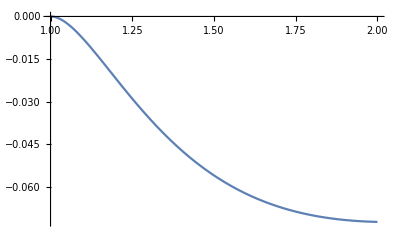

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
Plot[F[x,-x^4/(6 (-1+x))-0.1],{x,1,2}, PlotRange->Automatic]
```